```mathematica
Table[Length[FindFullFormula4[CycleGraph[k]]],{k,3,10}]
```

{0,1,5,20,70,231,735,2290}

```mathematica
Table[FindFullFormula4[CycleGraph[k]],{k,3,6}]
```

{{},{v1x2x3x4},{v1x2x35x4,v1x25x3x4,v1x24x3x5,v14x2x3x5,v13x2x4x5},{v1x2x35x46,v1x26x35x4,v1x25x3x46,v1x25x36x4,v1x246x3x5,v1x24x36x5,v1x24x35x6,v15x2x3x46,v15x2x36x4,v15x26x3x4,v15x24x3x6,v14x2x36x5,v14x2x35x6,v14x26x3x5,v14x25x3x6,v135x2x4x6,v13x2x46x5,v13x26x4x5,v13x25x4x6,v13x24x5x6}}

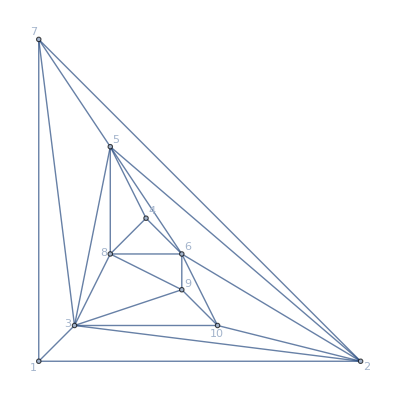

```mathematica
Graph[ReadGrof[100],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

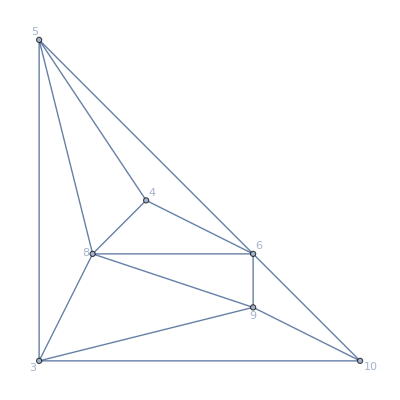

```mathematica
Graph[VertexDelete[ReadGrof[100],{1,2,7}],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

```mathematica
FilterSymbol[sym_,vertices_]:=Block[{v2=SymbolToSets[sym]},
v2=Map[Select[#,MemberQ[vertices,#]&]&,v2];
v2=Select[v2,#≠{}&];
v2=Sort[Map[Sort[#]&,v2],Min[#1]<Min[#2]&];
SetsToSymbol[v2]
]
```

```mathematica
FilterSymbol[v36x49x5x8a,{3,6,5,10}]
```

v36x5xa

```mathematica
Map[FilterSymbol[#,{3,6,5,10}]&,FindFullFormula4[VertexDelete[ReadGrof[100],{1,2,7}]]]
```

{v3x5x6xa,v36x5xa,v36x5xa,v36x5xa,v36x5a}

```mathematica
Map[FilterSymbol[#,{3,6,5,10}]&,FindFullFormula4[VertexDelete[ReadGrof[100],{4,9,8}]] ]
```

{v3x5ax6,v36x5a,v36x5xa}

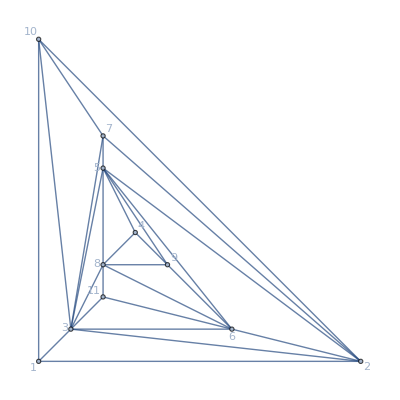

```mathematica
Graph[ReadGrof[1000],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

```mathematica
Map[FilterSymbol[#,{3,6,5,10}]&,FindFullFormula1234[VertexDelete[ReadGrof[1000],{1,2,7,10}]]]
```

{v3x5x6}

```mathematica
VertexDelete[Graph[ReadGrof[1000],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"],{1,2,10}]//FindFullFormula1234
```

{v39x46x5bx78,v39x467x5bx8}

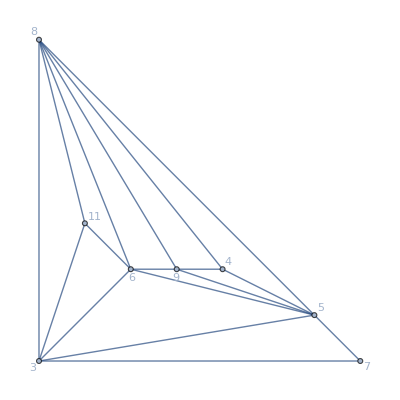

```mathematica
VertexDelete[Graph[ReadGrof[1000],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"],{1,2,10}]
```

```mathematica
Graph[ReadGrof[1000],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]//FindFullFormula1234
```

{v1467x28x39x5ab}